Importamos datos de experimento LUX vs Mh1

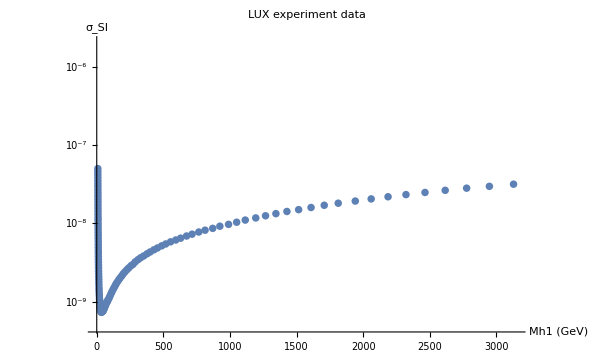

```mathematica
LUX=Import["/home/felipe/Documents/Programas/micromegas_4.1.8/2IHDM/scan_final/scan_rand_1.5TeV/LUX/LUX.dat"];
ListLogPlot[LUX,AxesLabel->{"Mh1 (GeV)","σ_SI"},PlotLabel->"LUX experiment data"]
```

### Hacemos Interpolación de los puntos a la función fLUX

```mathematica
fLUX=Interpolation[LUX]
```

InterpolatingFunction[{{8.06079, 4832.31}}, <>]

### Graficamos la función fLUX

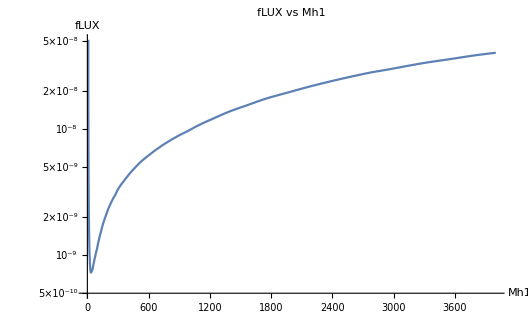

```mathematica
LogPlot[fLUX[x],{x,8.07,4000},PlotRange->{5*10^-10,5.1*10^-8},Epilog->Map[Point, LUX],PlotLabel->"fLUX vs Mh1",AxesLabel->{"Mh1","fLUX"}]
```

### Importamos columna Mh1 a partir de los datos de scan_rand_1TeV.dat

```mathematica
CMh1={#[[1]]}&/@Import["/home/felipe/Documents/Programas/micromegas_4.1.8/2IHDM/scan_final/scan_rand_1.5TeV/scan_rand_1.5TeV.dat"];
```

### Creamos una lista con el valor que toma la función fLUX para cada valor de Mh1

```mathematica
Lista1=fLUX[CMh1]
```

InterpolatingFunction::nomthd: There is no method "Mh1" for InterpolatingFunction objects.

{{InterpolatingFunction[{{8.06079, 4832.31}}, <>][Mh1]},{1.22327×10^-8},{1.10814×10^-8},{1.04792×10^-8},{1.16392×10^-8},{1.1606×10^-8},585793,{1.07521×10^-8},{1.05682×10^-8},{1.04042×10^-8},{1.17366×10^-8},{1.06331×10^-8}}
 |  |  |  |

### Exportamos la Lista1 con los datos

```mathematica
Export["/home/felipe/Documents/Programas/micromegas_4.1.8/2IHDM/scan_final/scan_rand_1.5TeV/LUX/fLUX_scan_rand_1.5TeV.dat",Lista1]
```

/home/felipe/Documents/Programas/micromegas_4.1.8/2IHDM/scan_final/scan_rand_1.5TeV/LUX/fLUX_scan_rand_1.5TeV.dat